# Tarea 3

## Método de Newton-Rhapson

Primero definimos la función a resolver. Se desea encontrar las raíces de f(x) = x^2-Cos(x) = 0.

```mathematica
f[x_]:=x^2-Cos[x];
```

Se define una función que realiza un paso del método de Newton-Rhapson:

```mathematica
NewtonRhapsonStep[x_]:=x-f[x]/f'[x];
```

Ejemplo de uso:

```mathematica
NewtonRhapsonStep[0.5]
```

0.924207

Repitiendo n veces el procedimiento y guardando las soluciones obtenemos las iteraciones del método de NR.

```mathematica
NewtonRhapson[x0_,n_]:=Block[{soluciones = {x0},x = x0},
Do[
x = NewtonRhapsonStep[x];
AppendTo[soluciones,x]; (* Añado el nuevo x a la lista *)
,
n (* Número de repeticiones *)
];

soluciones
];
```

Ejemplo de soluciones:

```mathematica
listaDeSoluciones = NewtonRhapson[0.2,10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

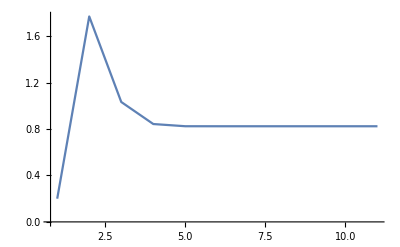

```mathematica
ListLinePlot[listaDeSoluciones,PlotRange->All]
```

## Tarea:

Definir la función para medir la razón de errores entre pasos:

```mathematica
Error(Subscript[x, k+1]) = Subscript[Δϵ, k+1]/(Δ Subscript[ϵ, k])^2≃ - (f''(Subscript[x, k+1]))/(f'(Subscript[x, k+1]))
```

y evaluar en los puntos de la lista de soluciones. Graficar el resultado.

Hint: Para evaluar una función con los elementos de una lista es usual utilizar los mapeos. Map[g, {a,b,c,d}] aplica la función g sobre cada uno de los elementos de la lista {a,b,c,d}.

```mathematica
Map[g,{a,b,c,d}]
```

{g[a],g[b],g[c],g[d]}